```mathematica
p1[x_]:=0.5(x^2-x)
p2[x_]:=-x^2+1.
p3[x_]:=0.5(x^2+x)
```

```mathematica
P=Transpose[{{0.5,-0.5,0},{-1,0,1},{0.5,0.5,0}}]
```

{{0.5,-1,0.5},{-0.5,0,0.5},{0,1,0}}

```mathematica
Inverse[P].{0,1,0}
```

{-1.,0.,1.}

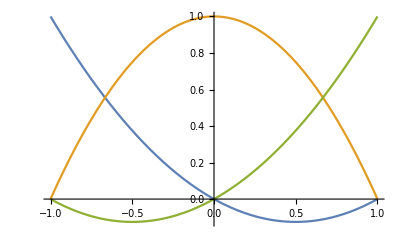

```mathematica
Plot[{p1[x],p2[x],p3[x]},{x,-1,1}]
```

```mathematica
F[x_]:=Exp[-0.03p1[x]+0.2p2[x]+0.2p3[x]]
```

```mathematica
Integrate[p1[x],{x,-1,1}]
Integrate[p2[x],{x,-1,1}]
Integrate[p3[x],{x,-1,1}]
```

0.333333

1.33333

0.333333

```mathematica
xloc={-1.,-0.6547,0,0.6547,1.}
wi={0.1000,0.5444,0.7111,0.5444,0.1000}
Fv=F[1]
```

{-1.,-0.6547,0,0.6547,1.}

{0.1,0.5444,0.7111,0.5444,0.1}

1.2214

```mathematica
Integrate[F[x]*p3[x]*p3[x],{x,-1,1}]
```

0.329821